## Introduction

Look for symmetric solutions when E > 0

## Symmetric solution

Search for x_+=θ_+ My previous analysis suggested this is indeed a solution.

### Define ODEs

```mathematica
Clear[b,j,k]
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->k/.b->1;

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//Simplify;
TableForm[J]
```

Sin[xm] Sin[xp] | -Cos[xm] Cos[xp] | 0 | 0
-Cos[xm] Cos[xp] | -k Cos[2 xm] Cos[2 θm]+Sin[xm] Sin[xp] | 0 | k Sin[2 xm] Sin[2 θm]
0 | 0 | Sin[θm] Sin[θp] | -Cos[θm] Cos[θp]
0 | k Sin[2 xm] Sin[2 θm] | -Cos[θm] Cos[θp] | -k Cos[2 xm] Cos[2 θm]+Sin[θm] Sin[θp]

```mathematica
subsymm={xp->p,θp->p,xm-> m,θm->m};
```

```mathematica
es1=es/.subsymm//Simplify;
TableForm[es1]
```

e-Cos[p] Sin[m]
-1/4 k Sin[4 m]-Cos[m] Sin[p]
e-Cos[p] Sin[m]
-1/4 k Sin[4 m]-Cos[m] Sin[p]

### Find FP

```mathematica
fpsymm=Solve[es1==0,{p,m}]/.C[1]->0/.C[2]->0;
Length[fpsymm]
```

20

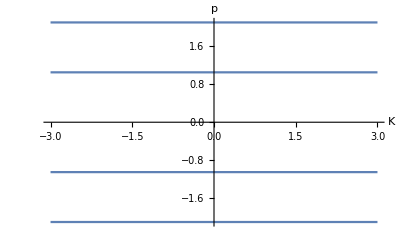

```mathematica
Plot[p/.fpsymm[[1;;10]]/.e->0.5,{k,-3,3},AxesLabel->{"K","p"},LabelStyle->15]
```

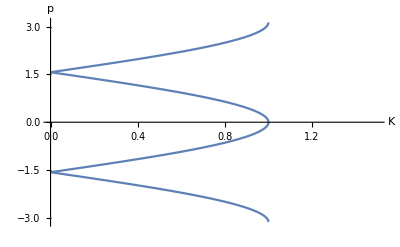

```mathematica
Plot[p/.fpsymm[[1;;10]]/.k->2,{e,0,1.5},AxesLabel->{"K","p"},LabelStyle->15]
```

```mathematica
TableForm[fpsymm[[1;;4]]]
```

p→ArcTan[-e,-√(1-e^2)] | m→-π/2
p→ArcTan[-e,√(1-e^2)] | m→-π/2
p→ArcTan[e,-√(1-e^2)] | m→π/2
p→ArcTan[e,√(1-e^2)] | m→π/2

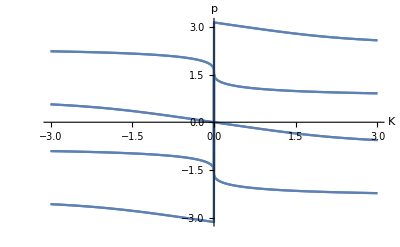

```mathematica
Plot[p/.fpsymm[[10;;-1]]/.e->0.5,{k,-3,3},AxesLabel->{"K","p"},LabelStyle->15]
```

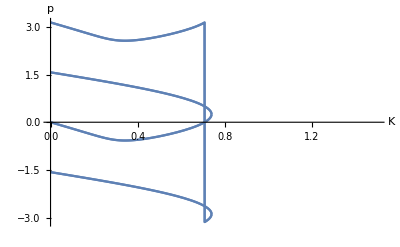

```mathematica
Plot[p/.fpsymm[[10;;-1]]/.k->2,{e,0,1.5},AxesLabel->{"K","p"},LabelStyle->15]
```

### RH -- compute and plot for all solution

Greater::nord: Invalid comparison with 0.93149+1.03391 ⅈ attempted.

Greater::nord: Invalid comparison with -3.036-5.64399 ⅈ attempted.

Greater::nord: Invalid comparison with 3.66801+7.37343 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

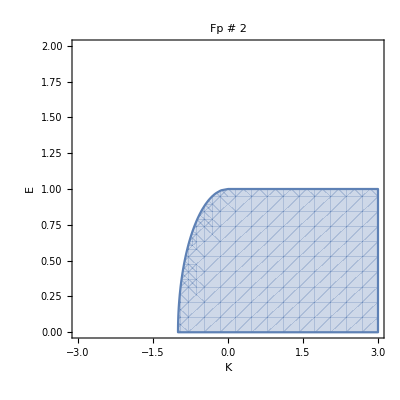
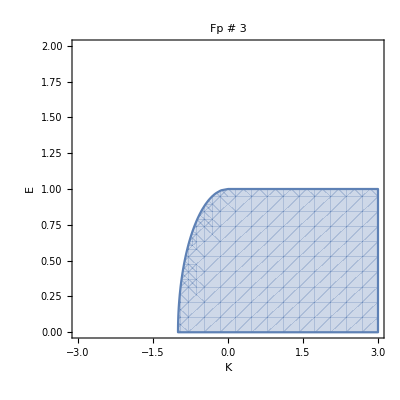
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Clear[λ];
chareqn=Collect[Det[J-λ IdentityMatrix[4]],λ,Simplify];
(*{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ]/.subsymm/.fpsymm[[1]]//Simplify;*)
{a0,a1,a2,a3,a4}=CoefficientList[chareqn,λ]/.subsymm/.fpsymm[[i]];

p1=RegionPlot[
a0>0&&
a1>0&&
a2>0&&
a3>0&&
a4>0&&
a3 a2 a1>a1^2+a3^2 a0,
{k,-3,3},{e,0,2},
FrameLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotLabel->"Fp # "<>ToString[i]
];
p1,
{i,1,20}
]
```

### First 4 solutions -- look at λ’s to be sure

```mathematica
TableForm[fpsymm[[1;;4]]]
```

p→ArcTan[-e,-√(1-e^2)] | m→-π/2
p→ArcTan[-e,√(1-e^2)] | m→-π/2
p→ArcTan[e,-√(1-e^2)] | m→π/2
p→ArcTan[e,√(1-e^2)] | m→π/2

```mathematica
Clear[λ];
chareqn=Collect[Det[J-λ IdentityMatrix[4]],λ,Simplify]/.subsymm/.fpsymm[[1]]
{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ]/.subsymm/.fpsymm[[1]]//Simplify;
TableForm[{a4,a3,a2,a1,a0}]
```

-√(1-e^2) (√(1-e^2) (-1+e^2)+2 (1-e^2) k-√(1-e^2) k^2)+(-4 (1-e^2)^(3/2)+6 (1-e^2) k-2 √(1-e^2) k^2) λ+(6 (1-e^2)-6 √(1-e^2) k+k^2) λ^2+(-4 √(1-e^2)+2 k) λ^3+λ^4

(-1+e^2) (-1+e^2+2 √(1-e^2) k-k^2)
-2 (2 (1-e^2)^(3/2)-3 k+3 e^2 k+√(1-e^2) k^2)
6-6 e^2-6 √(1-e^2) k+k^2
-4 √(1-e^2)+2 k
1

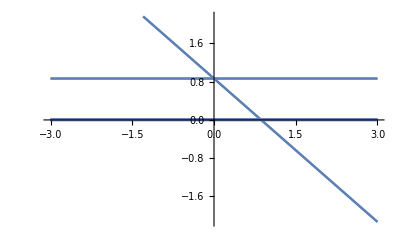
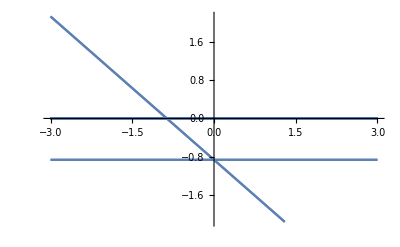
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
λ=J/.subsymm/.fpsymm[[i]];
Plot[λ/.e->0.5,{k,-3,3}],
{i,1,4}
]
```

```mathematica
alllams=λ=J/.subsymm/.fpsymm[[{3,4}]]//Flatten//DeleteDuplicates
```

{-√(1-e^2),0,-√(1-e^2)-k,√(1-e^2),√(1-e^2)-k}

```mathematica
Table[Solve[alllams[[i]]==0],{i,1,Length[alllams]}]
```

{{{e→-1},{e→1}},{{}},{{k→-√(1-e^2)}},{{e→-1},{e→1}},{{k→√(1-e^2)}}}

So one of these is the condition. From the plots above, it is  k→-√(1-e^2)

```mathematica
fpsymm[[1;;4]]//TableForm
```

p→ArcTan[-e,-√(1-e^2)] | m→-π/2
p→ArcTan[-e,√(1-e^2)] | m→-π/2
p→ArcTan[e,-√(1-e^2)] | m→π/2
p→ArcTan[e,√(1-e^2)] | m→π/2

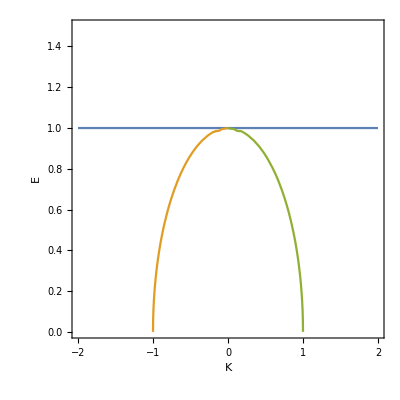

```mathematica
ContourPlot[{e==1,k==-√(1-e^2),k==√(1-e^2)},{k,-2,2},{e,0,1.5},FrameLabel->{"K","E"},LabelStyle->15]
```

## Bifucations (work in progress)

### Find SN

```mathematica
fpsymm[[2]]
```

{p→ArcTan[-e,√(1-e^2)],m→-π/2}

#### First general the RH coefficients

```mathematica
Clear[λ];
chareqn=Collect[Det[J-λ IdentityMatrix[4]],λ,Simplify];
{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ]/.subsymm/.fpsymm[[2]]//Simplify;
TableForm[{a0,a1,a2,a3,a4}]
```

1
2 (2 √(1-e^2)+k)
6-6 e^2+6 √(1-e^2) k+k^2
2 (2 (1-e^2)^(3/2)+3 k-3 e^2 k+√(1-e^2) k^2)
(-1+e^2) (-1+e^2-2 √(1-e^2) k-k^2)

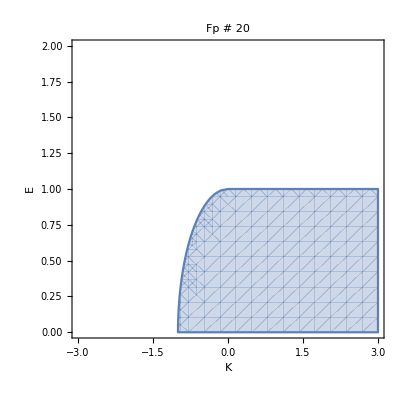

```mathematica
p1=RegionPlot[
a0>0&&
a1>0&&
a2>0&&
a3>0&&
a4>0&&
a1 a2-a0 a3>0&&
a1 a2 a3-a1^2 a4-a0 a3^2>0,
{k,-3,3},{e,0,2},
FrameLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotLabel->"Fp # "<>ToString[i]
]
```

```mathematica
Δ1=a1;
Δ2=Det[{{a1,a0},{a3,a2}}]//Simplify;
Δ3=Det[{{a1,a0,0},{a3,a2,a1},{0,a4,a3}}]//Simplify;
Δ4=Det[{{a1,a0,0,0},{a3,a2,a1,a0},{0,a4,a3,a2},{0,0,0,a4}}]//Simplify;
```

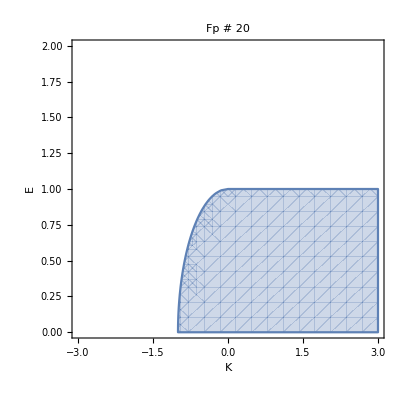

```mathematica
p1=RegionPlot[
Δ1>0&&
Δ2>0&&
Δ3>0&&
Δ4>0,
{k,-3,3},{e,0,2},
FrameLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotLabel->"Fp # "<>ToString[i]
]
```